```mathematica
SetDirectory[NotebookDirectory[]];
exclCurves=Import["Exclusion-Curves/exclCurves.m"];
rescale={#⟦1⟧,1.97 10^-9#⟦2⟧}&;
Do[
Do[
Do[
exclCurves[expt][shape][flav]=rescale/@exclCurves[expt][shape][flav],{flav,Keys@exclCurves[expt][shape]}
 ],
{shape, Keys@exclCurves[expt]} 
 ]
,{expt,Keys@exclCurves}
]
Γ=(d^2 mN^3)/(4π);
decEqRadEarth= Assuming[{mN>0,d>0},d/.Solve[197/Γ==6.4 10^3(*km*)* 10^18 (* fm/km *),d]⟦2⟧//Quiet]
```

(6.21939×10^-10)/mN^(3/2)

## Flavor Dependence

```mathematica
toPlot=Flatten[Table[ Table[exclCurves[expt]["Box"][flav],{flav,{"e","μ","τ"}}],{expt,Keys@exclCurves}],1];
```

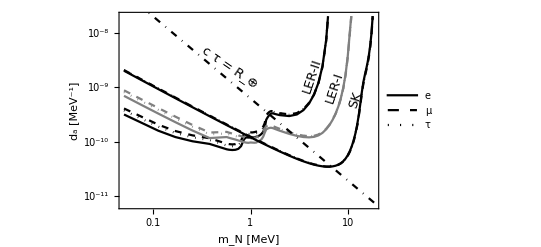

```mathematica
p1=ListLogLogPlot[toPlot,PlotRange->{0.7 10^-11,2 10^-8},Joined->True,Frame-> True,FrameStyle->Black,PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Gray,{Gray,Dashed},{Gray,Dotted}},
Epilog->{Inset[Rotate[Style["c τ = R_⊕",13],-0.6],{-0.48,-19.85}],Inset[Rotate[Style["SK",13],1.25],{2.48,-21.25}],Inset[Rotate[Style["LER-I",13],1.25],{2,-20.75}],Inset[Rotate[Style["LER-II",13],1.25],{1.45,-20.25}]},PlotLegends->Placed[{"e","μ","τ"},{0.12,0.175}],FrameLabel->(Style[#,14]&)/@{"m_N   [MeV]","d_a    [MeV^-1]"},PlotRangePadding->0]//Quiet;
p2=LogLogPlot[decEqRadEarth,{mN,0.05,18.8},FrameStyle->Black,PlotStyle->{{Black,DotDashed}},
FrameLabel->(Style[#,14]&)/@{"m_N   [MeV]","d_a    [MeV^-1]"},PlotRangePadding->0];
fig1=Show[p1,p2]
```

```mathematica
Export["PDFs/Flavor-sensitivity.pdf",fig1];
```

## Shape Dependence

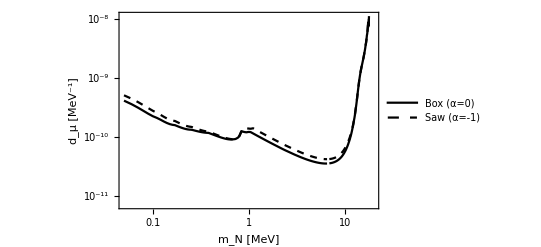

```mathematica
toPlot={Table[{mN,Min[Table[Interpolation[exclCurves[expt]["Box"]["μ"],InterpolationOrder->2][mN] ,{expt,Keys@exclCurves}]]},{mN,0.05,18.7,0.01}]//Quiet,Table[{mN,Min[Table[Interpolation[exclCurves[expt]["Saw"]["μ"],InterpolationOrder->2][mN] ,{expt,Keys@exclCurves}]]},{mN,0.05,18.7,0.01}]}//Quiet ;
p1=ListLogLogPlot[toPlot,PlotRange->{{0.05,20},{0.7 10^-11,1.1 10^-8}},Joined->True,Frame-> True,FrameStyle->Black,PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Gray,{Gray,Dashed},{Gray,Dotted}},
PlotLegends->Placed[{"Box (α=0)", "Saw (α=-1)"},{0.2,0.8}],PlotRangePadding->0,FrameLabel->(Style[#,14]&)/@{"m_N   [MeV]","d_μ    [MeV^-1]"},PlotRangePadding->0]//Quiet
```

```mathematica
Export["PDFs/Shape-sensitivity.pdf",p1];
```